```mathematica
ClearAll["Global`*"]
ϵ=(1-e1)*(1-e2)-e1*e2;
Pocg=ϵ*g/(ϵ*g +e2*(1-g));
Podg=(1-ϵ)*g/((1-ϵ)*g+(1-e2)*(1-g));
Pocb=e2*g/(e2*g+(1-e2)*(1-g));
Podb=(1-e2)*g/((1-e2)*g+e2*(1-g));
```

```mathematica
Picg=ϵ*Pocg+(1-ϵ)*Podg;
Pidg=(1-e2)*Podg+e2*Pocg;
Picb=ϵ*Pocb+(1-ϵ)*Podb;
Pidb=(1-e2)*Podb+e2*Pocb;
```

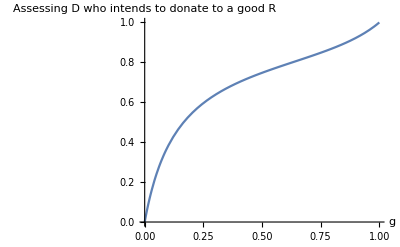

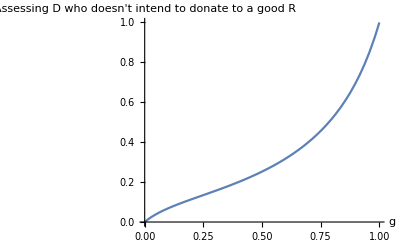

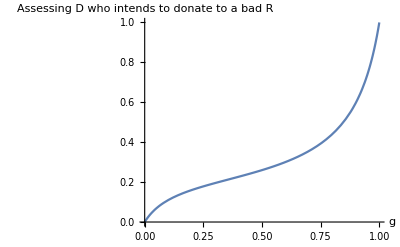

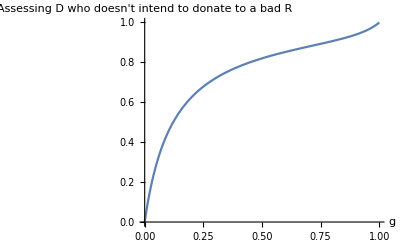

```mathematica
(* Plots for the assessment rules given a donor's intention *)
Plot[Picg/.{e1->0.01,e2-> 0.01},{g,0,1},PlotRange->{0,1},AxesLabel->{g,Style["Assessing D who intends to donate to a good R",Italic]}]
Plot[Pidg/.{e1-> 0.01,e2-> 0.01},{g,0,1},PlotRange->{0,1},AxesLabel->{g,Style["Assessing D who doesn't intend to donate to a good R",Italic]}]
Plot[Picb/.{e1-> 0.01,e2-> 0.01},{g,0,1},PlotRange->{0,1},AxesLabel->{g,Style["Assessing D who intends to donate to a bad R",Italic]}]
Plot[Pidb/.{e1-> 0.01,e2-> 0.01},{g,0,1},PlotRange->{0,1},AxesLabel->{g,Style["Assessing D who doesn't intend to donate to a bad R",Italic]}]
```

```mathematica
gzplus= x*(1-gz)*(gx2*Picg+(gx-gx2)*Pidb)
```

```mathematica
(* Solving the reputation dynamics *)
```